```mathematica
(* Extended power law model as currently in the paper *) 
(* Defined from hazard function k(τ) = α/τ with limits *)
kPow[τ_] = (α/(tauMin+τ))+(1/tauMax)
sol=DSolve[s'[τ] == -kPow[τ]* s[τ], 
Assumptions->{α>0, τ>0, tauMin>0,tauMax>0,tauMax>tauMin}]
sPowTmp[τ_]=s[τ]/. sol[[1]]
```

1/tauMax+α/(tauMin+τ)

{{s[τ]→ⅇ^(-τ/tauMax-α Log[tauMin+τ]) C[1]}}

ⅇ^(-τ/tauMax-α Log[tauMin+τ]) C[1]

```mathematica
(* Take the limit to get the constant *)
limitEq=Limit[sPowTmp[τ],τ->0,Assumptions->{α>0, tauMin>0,tauMax>0,tauMax>tauMin} ]==1;
solution=Solve[limitEq,C[1]]
sPow[τ_]=FullSimplify[sPowTmp[τ]/.solution]
```

{{C[1]→tauMin^α}}

{ⅇ^(-τ/tauMax) tauMin^α (tauMin+τ)^-α}

```mathematica
(* Tntegrate to get an expression for the turnover time .*)
TPow[τ_] = Integrate[sPow[τ], {τ,0,Infinity},Assumptions->{α>0, τ> 0, tauMin>0,tauMax>0,tauMax>tauMin} ]
```

{ⅇ^(tauMin/tauMax) tauMin ExpIntegralE[α,tauMin/tauMax]}

```mathematica
(* Inverse laplace transform to get p(k). note the singularity at k=k_min*)
p[k_,α_,tauMin_,tauMax_]=InverseLaplaceTransform[sPow[tau],tau,k]//FullSimplify
```

{(ⅇ^((-k+1/tauMax) tauMin) (k-1/tauMax)^(-1+α) tauMin^α HeavisideTheta[k-1/tauMax])/Gamma[α]}

```mathematica
(* Alternative form where we start with p(k) and impose a soft cutoff *) 
assume={α∈Reals,tauMin>0,tauMax>0,k>0, tau>0,tauMax>tauMin, kMax>0, kMin>0,kMax>kMin};

(* p(k) product of 3 factors: *)
powerLaw[k_,α_]:=k^(α-1);
fastCutoff[k_,kMax_]:=Exp[-k /kMax];          (* ~1 for k << kMax = 1/tauMin*)
slowCutoff[k_,kMin_]:=Exp[-kMin/k ];      (* ~1 for k >> kMin = 1/tauMax*)

pUnnorm[k_,α_,kMin_,kMax_]:=powerLaw[k,α] fastCutoff[k,kMax] slowCutoff[k,kMin];

(*Normalization:integrate the product over all k*)
Zgig=Integrate[pUnnorm[k,α,kMin,kMax],{k,0,Infinity},Assumptions->assume]//FullSimplify;
Zgig /.{kMin-> 1/tauMax,kMax-> 1/tauMin}//FullSimplify
(*expected:2 (tauMin tauMax)^(-α/2) BesselK[α,2 Sqrt[tauMin/tauMax]]*)

Z[α_,kMin_,kMax_]=Zgig; (*Set (=),not SetDelayed,so the integral is done once*)

pGIG[k_,α_,kMin_,kMax_]:=pUnnorm[k,α,kMin,kMax]/Z[α,kMin,kMax];
pGIG[k,α,kMin,kMax]/.{kMin-> 1/tauMax,kMax-> 1/tauMin}//FullSimplify
```

2 (1/(tauMax tauMin))^(α/2) BesselK[α,2 √(tauMin/tauMax)]

True

(ⅇ^(-1/(k tauMax)-k tauMin) k^(-1+α) (1/(tauMax tauMin))^(-α/2))/(2 BesselK[α,2 √(tauMin/tauMax)])

```mathematica
(*---builds on powerLaw,fastCutoff,slowCutoff,pUnnorm,Zgig from above---*)         
(*1. Survival function:Laplace transform of pGIG*)
sDirect=Integrate[pGIG[k,α,kMin,kMax] Exp[-k tau],{k,0,Infinity},Assumptions->assume]//FullSimplify

(*By inspection:Exp[-k tau] Exp[-k/kMax]=Exp[-k (1/kMax+tau)],so s(tau) is Z with kMax replaced by kMax/(1+kMax tau)*)
kMaxEff[tau_,kMax_]:=kMax/(1+kMax tau);
s[tau_,α_,kMin_,kMax_]:=Z[α,kMin,kMaxEff[tau,kMax]]/Z[α,kMin,kMax];

FullSimplify[sDirect==s[tau,α,kMin,kMax],assume]     (*True*)
FullSimplify[s[tau,α,kMin,kMax],assume]
(* ->(1+kMax tau)^(-α/2) BesselK[α,2 Sqrt[kMin (1/kMax+tau)]]/BesselK[α,2 Sqrt[kMin/kMax]]*)
```

((1+kMax tau)^(-α/2) BesselK[α,2 √(kMin (1/kMax+tau))])/BesselK[α,2 √(kMin/kMax)]

True

((1+kMax tau)^(-α/2) BesselK[α,2 √(kMin (1/kMax+tau))])/BesselK[α,2 √(kMin/kMax)]

```mathematica
(*2. Turnover time T=Integral of s;via E[1/k]=Z(alpha-1)/Z(alpha)*)Tdirect=Integrate[s[tau,α,kMin,kMax],{tau,0,Infinity},Assumptions->assume];        (*may stay unevaluated;the identity below gives it*)
T[α_,kMin_,kMax_]:=Z[α-1,kMin,kMax]/Z[α,kMin,kMax];
FullSimplify[T[α,kMin,kMax],assume]
(* ->BesselK[α-1,2 Sqrt[kMin/kMax]]/(Sqrt[kMin kMax] BesselK[α,2 Sqrt[kMin/kMax]])*)

(*Steady-state mean age=E[1/k^2]/E[1/k]*)
meanAge[α_,kMin_,kMax_]:=Z[α-2,kMin,kMax]/Z[α-1,kMin,kMax];

(*3. Numerical checks at the alpha=0.5 fit:tauMin~0.2041 yr,tauMax~1960 yr*)With[{a=0.5,k1=1/1960.,k2=1/0.2041},{NIntegrate[pGIG[k,a,k1,k2],{k,0,Infinity}],(*1*)NIntegrate[pGIG[k,a,k1,k2] Exp[-k 5.],{k,0,Infinity}],s[5.,a,k1,k2],(*equal*)NIntegrate[s[t,a,k1,k2],{t,0,Infinity},Method->"DoubleExponential"],T[a,k1,k2],(* ~20,twice*)meanAge[a,k1,k2]}]                                                          (* ~1000*)
```

BesselK[-1+α,2 √(kMin/kMax)]/(√(kMax kMin) BesselK[α,2 √(kMin/kMax)])

{1.,0.182329,0.182329,20.0009,20.0009,1000.}

k | shifted gamma diff | GIG diff
0.001 | 8.88178×10^-16 | 8.88178×10^-16
0.01 | 8.88178×10^-16 | 0.
0.1 | 0. | 0.
1. | 0. | 0.
10. | 4.44089×10^-16 | 0.

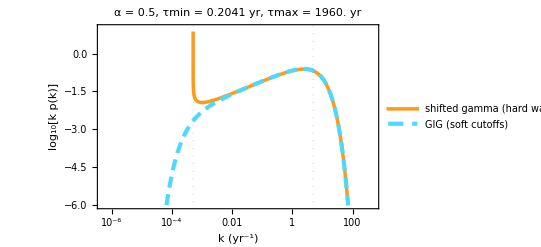

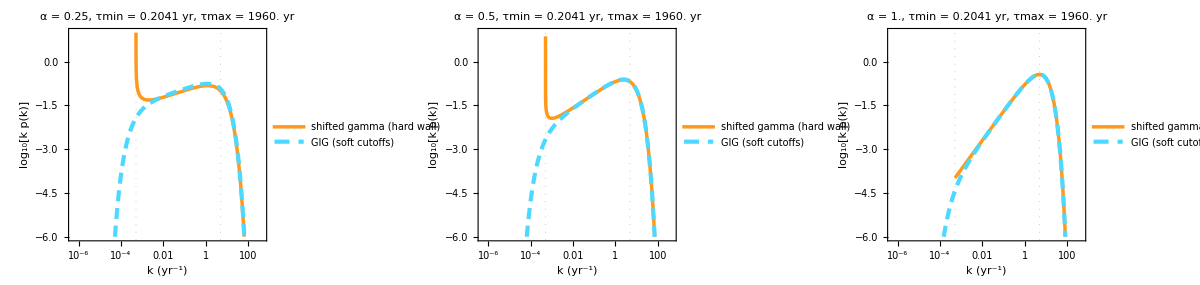

```mathematica
(* =====Plotting the derived densities in log space=====The notebook's derived expressions are p[k,alpha,tauMin,tauMax] (shifted gamma,from InverseLaplaceTransform)=tauMin^alpha (k-1/tauMax)^(alpha-1) Exp[-tauMin (k-1/tauMax)] HeavisideTheta[k-1/tauMax]/Gamma[alpha] pGIG[k,alpha,kMin,kMax] (soft cutoffs,normalized by Zgig)=k^(alpha-1) Exp[-k/kMax-kMin/k]/(2 (kMin kMax)^(alpha/2) BesselK[alpha,2 Sqrt[kMin/kMax]]) Plotting them directly fails numerically:below the wall (k-1/tauMax)^(alpha-1) is complex,and far past the fast cutoff the exponentials underflow.The functions below are Log[k p(k)] for those same expressions,written term by term:each Log[] of a product becomes a sum of logs,the Heaviside factor becomes the explicit support condition x>0,and Log[Gamma] becomes LogGamma.Each body is wrapped in parentheses so line breaks don't end the expression early.*)(*Log[k p[k,alpha,tauMin,tauMax]] for k>1/tauMax (outside the support:Indeterminate=gap)*)logqShift[k_?NumericQ,α_,tauMin_,tauMax_]:=With[{x=k-1/tauMax},If[x<=0,Indeterminate,(Log[k]                           (*density per ln k*)+α Log[tauMin]           (*tauMin^alpha*)+(α-1) Log[x]          (*(k-1/tauMax)^(alpha-1):power law from the wall*)-tauMin x                       (*Exp[-tauMin (k-1/tauMax)]:soft fast cutoff*)-LogGamma[α]             (*1/Gamma[alpha]*))]];

(*Log[k pGIG[k,alpha,kMin,kMax]]*)
logqGIG[k_?NumericQ,α_,kMin_,kMax_]:=(Log[k]                             (*density per ln k*)+(α-1) Log[k]            (*powerLaw*)-k/kMax                           (*fastCutoff*)-kMin/k                           (*slowCutoff*)-(Log[2]+(α/2) Log[kMin kMax]+Log[BesselK[α,2 Sqrt[kMin/kMax]]])   (*Log[Zgig]*));

(*-----Check:these equal Log of the notebook expressions where both can be evaluated-----*)
With[{a=0.5,t1=0.2041,t2=1960.},TableForm[Table[{k,logqShift[k,a,t1,t2]-Log[k p[k,a,t1,t2]],logqGIG[k,a,1/t2,1/t1]-Log[k pGIG[k,a,1/t2,1/t1]]},{k,{0.001,0.01,0.1,1.,10.}}],TableHeadings->{None,{"k","shifted gamma diff","GIG diff"}}]]
(*both difference columns should be~0 (rounding error only)*)

(*-----Plot-----*)
compareP[α_,tauMin_,tauMax_]:=Module[{kMin=1/tauMax,kMax=1/tauMin},LogLinearPlot[{logqShift[k,α,tauMin,tauMax]/Log[10],logqGIG[k,α,kMin,kMax]/Log[10]},{k,kMin/1000,100 kMax},PlotRange->{-6,1},PlotPoints->400,MaxRecursion->8,PlotStyle->{{AbsoluteThickness[2.5],RGBColor[1,0.6,0.1]},(*shifted gamma:orange*){AbsoluteThickness[3],Dashing[{0.02,0.012}],RGBColor[0.3,0.85,1]}},(*GIG:light cyan*)GridLines->{{kMin,kMax},None},GridLinesStyle->Directive[GrayLevel[0.6],Dotted],Frame->True,FrameStyle->GrayLevel[0.75],LabelStyle->GrayLevel[0.85],FrameLabel->{"k (\!\(\*SuperscriptBox[\(yr\), \(-1\)]\))","\!\(\*SubscriptBox[\(log\), \(10\)]\)[k p(k)]"},PlotLabel->Row[{"α = ",α,",  τmin = ",tauMin," yr,  τmax = ",tauMax," yr"}],PlotLegends->Placed[LineLegend[{"shifted gamma (hard wall)","GIG (soft cutoffs)"},LabelStyle->GrayLevel[0.85]],{Left,Top}]]];

compareP[0.5,0.2041,1960.]
GraphicsRow[compareP[#,0.2041,1960.]&/@{0.25,0.5,1.0},ImageSize->1200]
```